Measurement-Based Quantum Computation |

Elementary Building Blockpaclet:Q3/tutorial/MeasurementBasedScheme#1941831266 | CNOT Gatepaclet:Q3/tutorial/MeasurementBasedScheme#1795737724
Single-Qubit Rotationspaclet:Q3/tutorial/MeasurementBasedScheme#93421842 | Graph Statespaclet:Q3/tutorial/MeasurementBasedScheme#184730958

According to the fundamental postulates of quantum mechanics,  the quantum state of a system changes as a consequence of two different causes. One is the time-evolution governed by the Schrödinger equation. Both the dynamical and geometric schemes of quantum computation are inherently based on such time evolution.

The other cause for the change in quantum states is the collapse of the quantum states upon measurement, as dictated by Postulate 3. Can we use this collapse process for quantum computation as well? At first glance, it may look absurd when considering the uncontrollable and random nature of the collapse of quantum states upon measurement. Nevertheless, quantum computation has recently been shown to be possible just by employing measurements in different bases, provided the system is prepared in a special quantum state called the cluster state or, more generally, the graph state (Raussendorf and Briegel, 2001https://doi.org/10.1103/PhysRevLett.86.5188; Raussendorf et al., 2002https://doi.org/10.1080/09500340110107487). Such a scheme of quantum computation is the measurement-based quantum computation or one-way quantum computation. The reasoning behind the “one-way” nomenclature will become clear below. There are several technical methods to implement measurement-based quantum computation. Here, we introduce elementary ideas, and we refer interested readers to the aforementioned articles and their follow-up literature.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this documentation, symbol S will be used to refer to a quantum register of qubits. Similarly, symbol c will be used to denote a collection of complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Elementary Building Block

To get an idea of how the measurement-based scheme works, first consider a quantum circuit of the following simple form

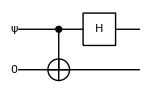
-Graphics-.

Here, the input state ψ=0 c_0+1 c_1 on the first qubit is arbitrary. Recall that the CNOT gate “copies” the computational basis states of the control qubit to the target qubit. It transforms the input state ψ⊗0  to

ψ=0⊗0 c_0+1⊗1 c_1.

Then, the additional Hadamard gate on the first qubit leads to the final state

1/2{0⊗ψ+1⊗(Ẑ ψ)} .

When the first qubit is measured, the state of the second qubit is set to different states depending on the measurement outcome. When the outcome is 0, the state is identical to the input state of the first qubit; and it is Zψ if the outcome is 1. In any case, the state coming out on the second qubit can be set to the (unknown) input state of the first qubit by applying an additional operation Z if necessary as in the following quantum circuit

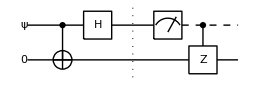
-Graphics-.

We can rewrite the above quantum circuit using relation between the CNOT and CZ gates into the following form

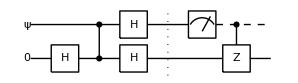
-Graphics-.

At this stage, there is no reason why we should prefer the CZ gate to the CNOT gate. However, we will see below that the CZ gate is better suited for the measurement-based scheme.

More importantly, the Hadamard gate followed by the measurement in the standard basis on the first qubit can be regarded as a measurement in the Pauli X basis. This has been made clearer in the following quantum circuit

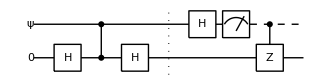
-Graphics-.

It is indeed physically achieved by rotating the measurement setup, as discussed in the tutorial “Computational Model of Measurement”.  In effect, the measurement in the Pauli X basis on the first qubit transfers a quantum state to the second qubit.

Next, let us consider a slightly different quantum circuit as follows.

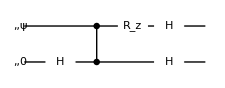
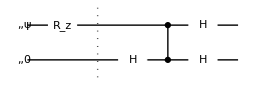
-Graphics-=-Graphics-

Compared to the previous quantum circuit, this has a single-qubit rotation U_z around the z-axis on the first qubit. In the above expression, the equality holds because U_z commutes with the CZ gate. Applying the previous result to the quantum circuit on the right-hand side immediately gives the output state

(0⊗((Û)_z ψ)+1⊗(Ẑ(Û)_z ψ))/(√2) .

Upon the measurement of the first qubit, the output state of the second qubit becomes either U_z ψ or  Z U_z ψ depending on the measurement outcome. In either case, the state  U_z ψ is achieved on the second qubit by applying an additional operation Z if necessary as follows.

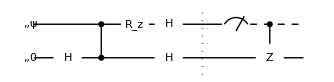

Again, the key point here is that the unitary operation U_z and the Hadamard gate followed by a measurement in the standard basis on the first qubit can be regarded as a measurement in the rotated basis. In the end, we have achieved the state with unitary gate U_z applied on it by means of a (rotated) measurement.

Since the Inverse of the Hadamard gate equals to the Hadamard gate itself, H^2=I, one can remove the second Hadamard gate on the second qubit by applying the Hadamard gate. This leads to the quantum circuit in Figure 1.

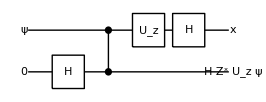

Figure 1. Elementary quantum circuit on which the measurement-based quantum computation is based. For the output, a summation over x=0,1 is assumed.

Accounting for the extra Hadamard gate that we applied, we obtain the output state

1/(√2)Σ_(x=0,1)x⊗(H Z^x U_z ψ)

for the quantum circuit in Figure 1. This quantum circuit requires no quantum gates once an entanglement has been created by the CZ gate, and only measurement is needed. The cost is that the Hadamard gate appears as a byproduct on the output qubit. However, we will see below that the trailing Hadamard gate on the second qubit plays an important role to achieve an arbitrary single-qubit rotation in the measurement-based scheme.

Single-Qubit Rotations

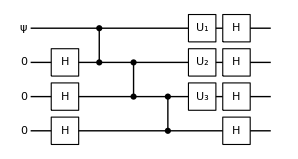

Figure 2. A preliminary quantum circuit to implement a single-qubit rotation by relying on measurement. The label U_j:=U_z(ϕ_j) denotes the single-qubit rotation around the z-axis by angle ϕ_j.

Let us now inspect the implementation of arbitrary single-qubit rotations solely based on measurement. Consider the quantum circuit in Figure 2. The output state from the quantum circuit can be analyzed by consecutively applying the result in Figure 1. It reads as

Σ_(x_1,x_2,x_3)x_1⊗x_2⊗x_3⊗(Z^x_3 U_z(ϕ_3)H Z^x_2 U_z(ϕ_2)H Z^x_1 U_z(ϕ_1)ψ) .

Using the identity H Z H=X, the final state on the fourth qubit can be written as

Ψ_4=Z^x_3 U_z(ϕ_3)X^x_2 U_x(ϕ_2)Z^x_1 U_z(ϕ_1)ψ .

Furthermore, using the identities X Z X=-Z and Z X Z=-X, we arrive at the expression

Ψ_4=Z^x_3 X^x_2 Z^x_1 U_z((-1)^x_2 ϕ_3)U_x((-1)^x_1 ϕ_2)U_z(ϕ_1)ψ .

The key point to notice here is that upon measurement on the first three qubits, the fourth qubit take on the state with a single-qubit rotation

U_z((-1)^x_2 ϕ_3)U_x((-1)^x_1 ϕ_2)U_z(ϕ_1)

operated on the initial state ψ of the first qubit. The rotation consists of three rotations around two perpendicular axes, and these are sufficient to realize any arbitrary single-qubit rotation (see tutorial “Single-Qubit Gates”).

The rotation achieved above through the quantum circuit in Figure 2 is not deterministic since the direction (clockwise or anti-clockwise) depends on outcomes x_1, x_2, and x_3 of the measurement on the first three qubits. However, we can make it deterministic by delaying the operations on the second qubit until after measurement on the first qubit and then operation on the third qubit until after measurement on the second qubit.

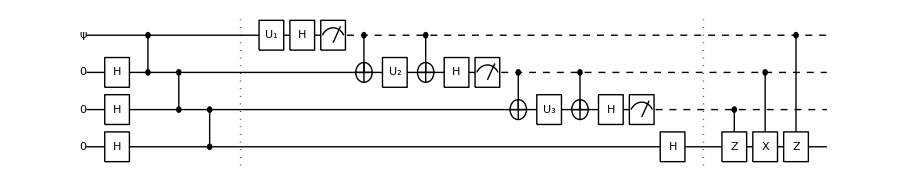

Figure 3. Quantum circuit to implement deterministically single-qubit rotation based on measurement (and classical feedback control). Notations are the same as in Figure 2. In many cases, the classical feedback controls (after then second vertical dotted line) on the forth qubit are not necessary.

Consider the modified quantum circuit in Figure 3. We first set ϕ_1=γ. Then, depending on the measurement outcome x_1 on the first qubit, we set ϕ_2=(-1)^x_1 β. Similarly, depending on the measurement outcome x_2 on the second qubit, we set ϕ_3=(-1)^x_2 α. The final state on the fourth qubit will become

Ψ_4=Z^x_3 X^x_2 Z^x_1 U_z(α)U_x(β)U_z(γ)ψ=Z^x_3 X^x_2 Z^x_1 U(α,β,γ)ψ

with the single-qubit Euler rotation U(α,β,γ) fixed deterministically. There are still undesired operations, Z^x_3 X^x_2 Z^x_1. However, these operations are irrelevant at the end of quantum computation, and do not have to be corrected. For example, if the final state is measured in the logical basis, Z does not affect the readout at all, and the effect of X can be handled by a classical post-processing. If really necessary, one can always remove them by further feedback controls as in the last part of the quantum circuit in Figure 3.

### Demonstration: R_Z(ϕ)

Although it is already clear that the elementary building block directly gives the rotation around the z-axis, we start the demonstration with it to establish a systematic way to achieve rotations around other axes. In this method, rotation around the z-axis is the simplest, the rotation around x-axis requires one more layer of measurements and feedback controls, and rotations around any other axes can be achieved through three layers of measurements and feedback controls.

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Real,c,ϕ]
```

Prepare the first qubit in an arbitrary initial state.

```mathematica
in=ProductState[S[1]->{c[0],c[1]},"Label"->Ket["ψ"]]
```

(c_(,,0) ,,0+c_(,,1) ,,1)_(S_(,,1))

Build the overall quantum circuit in two steps indicated by the vertical dashed line. The first step corresponds to the preparation, and the second to the operation.

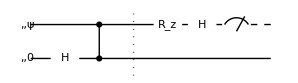

```mathematica
qc=QuantumCircuit[in,Ket[S@{2}],
S[{2},6],CZ[S[1],S[2]],"Separator",
Rotation[ϕ,S[1,3]],S[1,6],Measurement[S[1,3]]]
```

Add feedback controls In order to completely remove the undesired (yet non-troubling) operators.

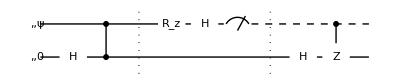

```mathematica
full=QuantumCircuit[qc,"Separator",
S[2,6],ControlledGate[S[1],S[2,3]]]
```

Calculate the output state. Below, the factor of √4 is for normalization. The above quantum circuit involves a measurement, and normalization is not guaranteed for exact vectors. Note that the first qubit end up in different state every time the above quantum circuit is run; and yet, the state on the second qubit is all the same regardless of the state of the first three qubits.

```mathematica
out=Elaborate[Sqrt[2]*full]//ExpToTrig//Garner
```

c_(,,0) 1_(,,S_(,,1))0_(,,S_(,,2)) (Cos[ϕ/2]-ⅈ Sin[ϕ/2])+c_(,,1) 1_(,,S_(,,1))1_(,,S_(,,2)) (Cos[ϕ/2]+ⅈ Sin[ϕ/2])

Compare the above result with the state obtained by directly applying the rotation around the z-axis.

```mathematica
new=Rotation[ϕ,S[1,3]]**in//Elaborate
```

c_(,,0) 0_(,,S_(,,1)) (Cos[ϕ/2]-ⅈ Sin[ϕ/2])+c_(,,1) 1_(,,S_(,,1)) (Cos[ϕ/2]+ⅈ Sin[ϕ/2])

```mathematica
KetMutate[KetDrop[out,S@{1}],S@{2}]-KetMutate[new,S@{1}]//FullGarner
```

0

### Demonstration: R_X(ϕ)

Prepare the first qubit in an arbitrary initial state.

```mathematica
in=ProductState[S[1]->{c[0],c[1]},"Label"->Ket["ψ"]]
```

(c_(,,0) ,,0+c_(,,1) ,,1)_(S_(,,1))

Build the overall quantum circuit in two steps indicated by the vertical dashed line. The first step corresponds to the preparation, and the second to the operation.

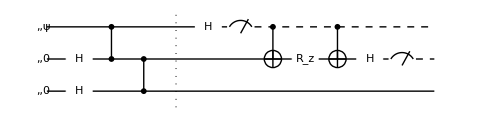

```mathematica
qc=QuantumCircuit[in,Ket[S@{2,3}],
S[{2,3},6],CZ[S[1],S[2]],CZ[S[2],S[3]],"Separator",
S[1,6],Measurement[S[1,3]],
CNOT[S[1],S[2]],Rotation[ϕ,S[2,3]],CNOT[S[1],S[2]],
S[2,6],Measurement[S[2,3]]]
```

Add feedback controls In order to completely remove the undesired (yet non-troubling) operators. Note that the feedback control elements may be simplified to one CNOT-like and one CZ-like feedback control, but here we keep them this way to show a regular pattern of feedback controls.

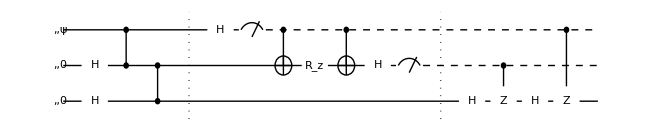

```mathematica
full=QuantumCircuit[qc,"Separator",
S[3,6],ControlledGate[S[2],S[3,3]],
S[3,6],ControlledGate[S[1],S[3,3]]]
```

Calculate the output state. Below, the factor of √4 is for normalization. The above quantum circuit involves measurement, and normalization is not guaranteed for exact vectors. Note that the first two qubits end up in different state every time the above quantum circuit is run; and yet, the state on the fourth qubit is all the same regardless of the state of the first three qubits.

```mathematica
out=Elaborate[Sqrt[4]*full]//ExpToTrig//Garner
```

1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3)) (c_(,,1) Cos[ϕ/2]-ⅈ c_(,,0) Sin[ϕ/2])+1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3)) (c_(,,0) Cos[ϕ/2]-ⅈ c_(,,1) Sin[ϕ/2])

Compare the above result with the state obtained by directly applying the Euler-like rotation.

```mathematica
new=Rotation[ϕ,S[1,1]]**in//Elaborate
```

1_(,,S_(,,1)) (c_(,,1) Cos[ϕ/2]-ⅈ c_(,,0) Sin[ϕ/2])+0_(,,S_(,,1)) (c_(,,0) Cos[ϕ/2]-ⅈ c_(,,1) Sin[ϕ/2])

```mathematica
KetMutate[KetDrop[out,S@{1,2}],S@{3}]-KetMutate[new,S@{1}]//FullGarner
```

0

### Demonstration: Euler Rotation, R_Z(ϕ_3)R_X(ϕ_2)R_Z(ϕ_1)

Prepare the first qubit in an arbitrary initial state.

```mathematica
in=ProductState[S[1]->{c[0],c[1]},"Label"->Ket["ψ"]]
```

(c_(,,0) ,,0+c_(,,1) ,,1)_(S_(,,1))

Build the overall quantum circuit in two steps indicated by the vertical dashed line. The first step corresponds to the preparation, and the second to the operation. Here, we use the abbreviated notation U_k:=U_Z(ϕ_k).

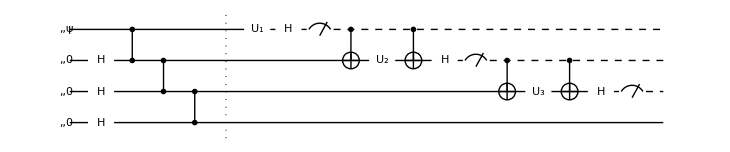

```mathematica
qc=QuantumCircuit[in,Ket[S@{2,3,4}],
S[{2,3,4},6],CZ[S[1],S[2]],CZ[S[2],S[3]],CZ[S[3],S[4]],"Separator",
Rotation[ϕ[1],S[1,3],"Label"->"U_1"],S[1,6],Measurement[S[1,3]],
CNOT[S[1],S[2]],Rotation[ϕ[2],S[2,3],"Label"->"U_2"],CNOT[S[1],S[2]],
S[2,6],Measurement[S[2,3]],
CNOT[S[2],S[3]],Rotation[ϕ[3],S[3,3],"Label"->"U_3"],CNOT[S[2],S[3]],
S[3,6],Measurement[S[3,3]]]
```

Add feedback controls In order to completely remove the undesired (yet non-troubling) operators.

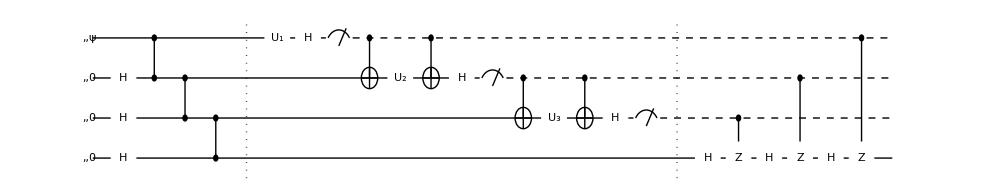

```mathematica
full=QuantumCircuit[qc,"Separator",
S[{4},6],ControlledGate[S[3],S[4,3]],
S[{4},6],ControlledGate[S[2],S[4,3]],
S[{4},6],ControlledGate[S[1],S[4,3]]]
```

Calculate the output state. Below, the factor of √8 is for normalization. The above quantum circuit involves measurement, and normalization is not guaranteed for exact vectors. Note that the first three qubits end up in different state every time the above quantum circuit is run; and yet, the state on the fourth qubit is all the same regardless of the state of the first three qubits.

```mathematica
out=Elaborate[Sqrt[8]*full]
```

1/2 ⅇ^(-1/2 ⅈ (ϕ_(,,1)+ϕ_(,,2)+ϕ_(,,3))) ((1+ⅇ^(ⅈ ϕ_(,,2))) c_(,,0)-ⅇ^(ⅈ ϕ_(,,1)) (-1+ⅇ^(ⅈ ϕ_(,,2))) c_(,,1)) 0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))+1/2 ⅇ^(-1/2 ⅈ (ϕ_(,,1)+ϕ_(,,2)-ϕ_(,,3))) (-((-1+ⅇ^(ⅈ ϕ_(,,2))) c_(,,0))+ⅇ^(ⅈ ϕ_(,,1)) (1+ⅇ^(ⅈ ϕ_(,,2))) c_(,,1)) 0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))

Compare the above result with the state obtained by directly applying the Euler-like rotation.

```mathematica
new=Rotation[ϕ[3],S[1,3]]**Rotation[ϕ[2],S[1,1]]**Rotation[ϕ[1],S[1,3]]**in//Elaborate
```

0_(,,S_(,,1)) (c_(,,1) Sin[(ϕ_(,,2))/2] (-ⅈ Cos[1/2 (ϕ_(,,1)-ϕ_(,,3))]+Sin[1/2 (ϕ_(,,1)-ϕ_(,,3))])+c_(,,0) Cos[(ϕ_(,,2))/2] (Cos[1/2 (ϕ_(,,1)+ϕ_(,,3))]-ⅈ Sin[1/2 (ϕ_(,,1)+ϕ_(,,3))]))+1_(,,S_(,,1)) (c_(,,0) Sin[(ϕ_(,,2))/2] (-ⅈ Cos[1/2 (ϕ_(,,1)-ϕ_(,,3))]-Sin[1/2 (ϕ_(,,1)-ϕ_(,,3))])+c_(,,1) Cos[(ϕ_(,,2))/2] (Cos[1/2 (ϕ_(,,1)+ϕ_(,,3))]+ⅈ Sin[1/2 (ϕ_(,,1)+ϕ_(,,3))]))

```mathematica
KetMutate[KetDrop[out,S@{1,2,3}],S@{4}]-KetMutate[new,S@{1}]//FullGarner
```

0

CNOT Gate

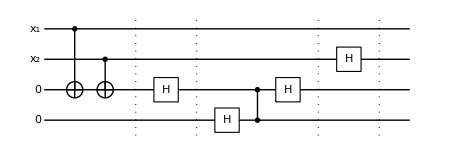

Figure 4. A primitive quantum circuit to implement the CNOT gate relying on measurement.

Let us now construct a quantum circuit to implement a CNOT gate in the measurement-based scheme. There are several ways to do so, and here we adopt the example described by the quantum circuit in Figure 4. The first two CNOT gates brings the input state to

x_1⊗x_2⊗x_1⊕x_2⊗0

at the instant indicated by the first vertical dotted line. At the second vertical dotted line, the state becomes

x_1⊗x_2⊗(Hx_1⊕x_2)⊗0 .

Now we use Figure 1, in effect, to transfer the state stored in the third qubit to the fourth qubit. This leads to the state

Σ_y_3 x_1⊗x_2⊗y_3⊗(H Z^y_3 Hx_1⊕x_2)=Σ_y_3 x_1⊗x_2⊗y_3⊗(X^y_3 x_1⊕x_2) .

Finally, applying the Hadamard gate on the second qubit leads to

Σ_(y_2,y_3)x_1⊗y_2⊗y_3⊗(X^y_3 x_1⊕x_2)(-1)^(y_2 x_2) .

The phase factor −1 occurs when x_2=y_2=1. By inspection, one can see that the same factor arises when one applies Z on both the first and fourth qubits. This leads to the final state out of the quantum circuit as follows

Ψ_out=Σ_(y_2,y_3)(Z^y_2 x_1)⊗y_2⊗y_3⊗(X^y_3 Z^y_2 x_1⊕x_2) .

When one performs measurement on the second and third qubits, depending on the outcomes y_2 and y_3, the final state stored in the first and fourth qubits is given by

Ψ_out_14=(Z^y_2 x_1)⊗(X^y_3 Z^y_2 x_1⊕x_2) .

Let us ignore the byproduct operators, X and/or Z, for the moment. We then see that in this quantum circuit, the first qubit plays the role of control qubit. The input state of the target qubit is put in the second qubit, and the output state is supposed to appear in the fourth qubit.

Using the relation between the CZpaclet:Q3/ref/CZQ3 Package Symbol and CNOTpaclet:Q3/ref/CNOTQ3 Package Symbol gates, we can rewrite the quantum circuit in Figure 4 into the new form in Figure 5. It is clear that once the entanglement is generated among the four qubits, then it is sufficient to perform a measurement on the second and third qubits to implement the CNOT gate. One has to apply Z on both the first and fourth qubit when y_2=1 and X as well if y_3=1 as indicated in the final part after the vertical dotted line in Figure 5. But again, in many cases, the additional step is not necessary or can be done with simple classical post-processing.

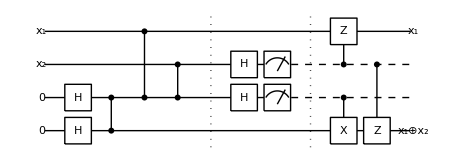

Figure 5. Quantum circuit to implement the CNOT gate based on measurement.

### Demonstration

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

The first qubit is the control qubit. The input state of the target qubit enters the second qubit and comes out on the forth qubit.

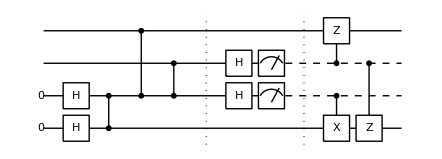

```mathematica
qc=QuantumCircuit[Ket[S@{3,4}],
S[{3,4},6],CZ[S[3],S[4]],CZ[S[1],S[3]],CZ[S[2],S[3]],"Separator",
S[{2,3},6],Measurement@S[{2,3},3],"Separator",
{ControlledGate[S[3],S[4,1]],
ControlledGate[S[2],S[1,3]]},
ControlledGate[S[2],S[4,3]]]
```

Observe how the logical basis states on the first two qubits are transformed to the first and forth qubit. The result is not exactly what we expect from the CNOT gate since we have not corrected the byproduct operators.

```mathematica
in=Basis[S@{1,2}];
out=qc**in;
Thread[in->out]//TableForm
```

0_S_10_S_2→0_S_10_S_20_S_30_S_4
0_S_11_S_2→0_S_11_S_21_S_31_S_4
1_S_10_S_2→1_S_11_S_20_S_31_S_4
1_S_11_S_2→1_S_11_S_20_S_30_S_4

Since the second and third qubits are not relevant, we can ignore them. Then, it is clearer that the operation indeed corresponds to the CNOT gate.

```mathematica
Thread[in->KetDrop[out,S@{2,3}]]//TableForm
```

0_S_10_S_2→0_S_10_S_4
0_S_11_S_2→0_S_11_S_4
1_S_10_S_2→1_S_11_S_4
1_S_11_S_2→1_S_10_S_4

Graph States

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

### Definition

Measurement-based quantum computation requires a crucial resource. A typical example is the state prepared by the quantum circuit elements to the left of the vertical dashed line in Figure 3. Once the state is prepared, from then on, quantum logic gates can be implemented solely by measurements in rotated bases. Such a state is called a graph state. Specifically, consider a graph 𝒢, where a set of vertices are connected by edges. A qubit is located at each vertex. Let U_(a b) denote the CZ gate on the two qubits located at  vertices a and b. To generate the graph state 𝒢 associated with the graph 𝒢, prepare each qubit first in the state +:=(0+1)/√2. Then, for each pair ⟨a b⟩ of vertices a and b connected by an edge, apply the CZ gate U_(a b) on the corresponding qubits. In short,

𝒢:=Π_⟨a b⟩U_ab+^(⊗n) ,

where the product is over all edges in graph 𝒢 and n is the number of vertices of 𝒢.

For example, consider a linear graph.

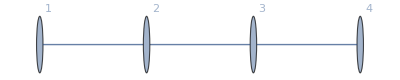

```mathematica
gr=Graph[{S[1]<->S[2],S[2]<->S[3],S[3]<->S[4]},VertexLabels->"Index"]
```

The corresponding graph state is created by the following quantum circuit model.

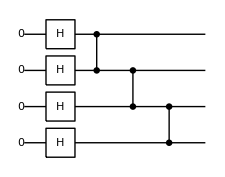

```mathematica
qc=QuantumCircuit[Ket[S@{1,2,3,4}],gr]
```

```mathematica
vec=Elaborate[qc]
```

-Graphics-

The same state can be directly obtained using GraphState.

```mathematica
new=GraphState[gr]
```

-Graphics-

```mathematica
vec-new//Simplify
```

0

### Correlation Operator

The graph states are not only useful as a valuable resource for measurement- based quantum computations, but they are also interesting in their own right. Graph states exhibit a high degree of entanglement. They have been studied extensively for the structure of bi-partite and multi-partite entanglement. One can also construct a class of quantum error-correction codes based on graph states. It allows for reliable storage and processing of quantum information in a fault-tolerant way.

All these features of graph states can be attributed to the following property: For each vertex a in a graph 𝒢, define an operator

C_a:=X_a Π_(b∈𝒩_a)Z_b,

where the product is over the set 𝒩_a of all vertices b connected to a. C_a is often called the correlation operator of vertex a. The graph state 𝒢 associated with 𝒢 is the unique simultaneous eigenstate with eigenvalue +1 of every C_a. In other words,

C_a 𝒢=𝒢

for all vertices a in the graph 𝒢. The operators C_a are said to stabilize the graph state. The stabilizer formalism provides powerful tools to exploit stabilizing operators.

As another example, consider the following graph and corresponding quantum circuit.

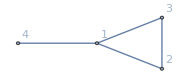

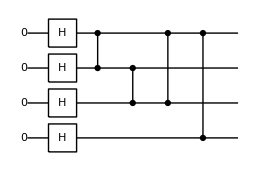

```mathematica
gr=Graph[{S[1]<->S[2],S[2]<->S[3],S[1]<->S[3],S[1]<->S[4]},ImageSize->Small,VertexLabels->"Index"]
QuantumCircuit[Ket[S@{1,2,3,4}],gr]
```

This is the graph state associated with the above graph.

```mathematica
vec=GraphState[gr]
```

-Graphics-

Here is the stabilizer subgroup associated with the above graph state; that is, the subgroup generated by the correlation operators.

```mathematica
stb=Stabilizer[gr]
```

-Graphics-

```mathematica
stb//PauliForm
```

{I⊗I⊗I⊗I,I⊗X⊗Z⊗X,I⊗Y⊗Y⊗I,I⊗Z⊗X⊗X,-(X⊗I⊗Y⊗Y),-(X⊗X⊗X⊗Z),-(X⊗Y⊗I⊗Y),X⊗Z⊗Z⊗Z,Y⊗I⊗Y⊗Z,-(Y⊗X⊗X⊗Y),Y⊗Y⊗I⊗Z,Y⊗Z⊗Z⊗Y,Z⊗I⊗I⊗X,Z⊗X⊗Z⊗I,Z⊗Y⊗Y⊗X,Z⊗Z⊗X⊗I}

The graph state is the unique simultaneous eigenstate with eigenvalue +1 of all correlation operators.

```mathematica
(stb**vec)/vec
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

### Graph vs Cluster States

Mathematically, one can associate a graph state with any graph. However, such a state is difficult to generate in practical systems. Doing so requires applying the CZ gate on spatially separated qubits. Cluster states are a special subclass of graph states, where the underlying graph is a d-dimensional square grid. The regular connectivity of the underlying graph makes the associated state far more feasible. Indeed, a number of physical methods have been proposed to generate cluster states.

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Computation: Models
▪Quantum Information Systems with Q3
▪Quick Quantum Computing with Q3

| Related Links
▪R. Raussendorf, D. Browne, and H. J. Briegel, Journal of Modern Optics 49, 1299 (2002)https://doi.org/10.1080/09500340110107487, "The one-way quantum computer--a non-network model of quantum computation (article)".
▪R. Raussendort and H. J. Briegel, Physical Review Letters 86, 5188 (2001)https://doi.org/10.1103/PhysRevLett.86.5188, "A One-Way Quantum Computer".
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).